```mathematica
SquareN[r_]:=4*Sum[Floor[Sqrt[r^2-x^2]], {x, 1, r-1}]
EdgeN[r_]:=4*Sum[Floor[Sqrt[r^2-x^2]]-Floor[Sqrt[r^2-(x+1)^2]]+1, {x, 1, r-1}] (*8*(r-1)*)
```

{0,1,8/3,4,6,22/3,60/7,41/4,12,69/5}

{0,8,16,24,32,40,48,56,64,72}

Plot::plln: Limiting value r in {x,0,r} is not a machine-sized real number.

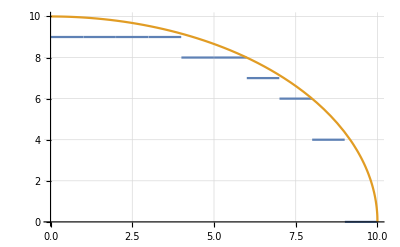

```mathematica
Table[SquareN[r]/(2*r), {r, 1, 10}]
Table[EdgeN[r], {r, 1, 10}]
ReplaceAll[Plot[{Floor[Sqrt[r^2-Ceiling[x]^2]], Sqrt[r^2-x^2]} , {x, 0, r}, GridLines->Automatic], r->10]
```

```mathematica
FindFit[Table[SquareN[r]/(2*r), {r, 1, 200}], a+b*x+c*Log[x], {a, b, c, d}, x]
```

{a→-2.03021,b→1.57179,c→-0.0439242,d→0.}